# Finding Periodic Sequences in 2D Smooth

For a function f:ℝ^2→ℝ^2  consider the sequence defined recursively by 
	p_(n+1)=f(p_n)
and an initial value p_0∈ℝ^2. We will make smoothness assumptions about f as we need them.  We learned that we will never see an unstable periodic orbit by iterating. We learned that a stable periodic orbit with a tiny stability region was also very hard to find!

Some pictures would probably help.   Friday’s pics were very boring. Lets look at some more interesting examples.

## Gingerbread Man Map

Even the simplest map can do interesting things.

```mathematica
f[{x_,y_}]:= {1-y+Abs[x], x }
ParametricPlot[{ f[{x,y}],{x,y}},{x,-2,8},{y,-2,8},
Mesh->All,
PlotRange->All]
ParametricPlot[{Nest[ f,{x,y},2],{x,y}},{x,-2,8},{y,-2,8},
Mesh->All,
PlotRange->All]
```

Lets see.

```mathematica
f[{x_,y_}]:= {1-y+Abs[x], x }
ListPlot[
Table[
x0=RandomReal[{-2,8},2];
NestList[f,x0,10^4],
{12}]
]
```

Lets see what happens with the holes.

```mathematica
h[ϵ_][x_]:= Which[
Abs[x]>ϵ, Abs[x],
Abs[x]≤ϵ, ϵ/2 + x^2/(2 ϵ)]
Plot[ {x^2,Abs[x], h[0.1][x]},{x, -1,1}]
```

```mathematica
f[{x_,y_}]:= {1-y+h[0.001][x], x }
ListPlot[
Table[
x0=RandomReal[{-2,8},2];
NestList[f,x0,10^4],
{12}]
]
```

```mathematica
FindRoot[Nest[ f,{x,y},5]=={x,y},{{x,-1.2},{y,-0.8}}]
FindRoot[Nest[ f,{x,y},10]=={x,y},{{x,-1.2},{y,-0.8}}]
```

```mathematica
FindRoot[Nest[ f,{x,y},15]=={x,y},{{x,-1.2},{y,-0.8}}]
FindRoot[Nest[ f,{x,y},20]=={x,y},{{x,-1.2},{y,-0.8}}]
FindRoot[Nest[ f,{x,y},30]=={x,y},{{x,-1.2},{y,-0.8}}]
FindRoot[Nest[ f,{x,y},50]=={x,y},{{x,-1.2},{y,-0.8}}]
```

```mathematica
NestList[ f,{-1,-1},5]
```

## Henon

Even the simplest map can do interesting things.

```mathematica
f[a_,b_][{x_,y_}]:= {1-a x^2+y, b x }
ParametricPlot[{ f[1.4,0.3][{x,y}],{x,y}},{x,-2,8},{y,-2,8},
Mesh->All,
PlotRange->{{-6,10},{-2,2}}]
SecPic=ParametricPlot[{ Nest[f[1.4,0.3],{x,y},2],{x,y}},{x,-2,8},{y,-2,8},
Mesh->All,
PlotRange->{{-6,10},{-2,2}}]
```

Lets see.

```mathematica
x0=RandomReal[{-1,1},2];
a=1.4; b=0.3;
Show[SecPic, 
ListPlot[NestList[f[a,b],x0,10^4],PlotStyle->Red]]
```

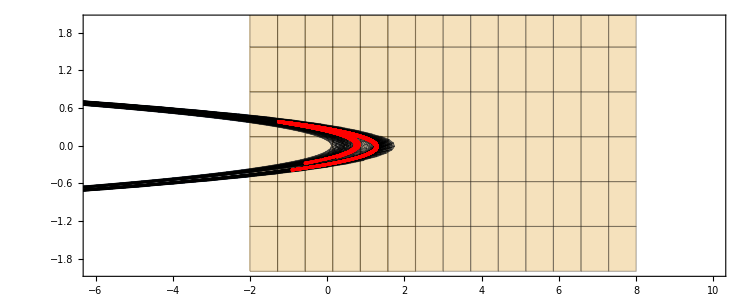

Lets see what happens with the holes.

```mathematica
ListPlot[NestList[f[a,b],x0,10^6],PlotStyle->Red]
```

# Building Simple Maps in 2D Non Smooth

The first thing we are going to look at is the puff pastry map a.k.a the Bakers map

## Bakers Map

This is a non-smooth map that is easy to understand.  It is puff pastry with a sharp knife.

```mathematica
Baker[{x_,y_}]:= Which[
0≤x<1/2, {2 *x,y/2},
1/2≤x≤1,{2-2 x, 1-y/2}
]
Vcolor=Function[{x,y,u,v}, Hue[u]];
Hcolor=Function[{x,y,u,v}, Hue[v]];
SetOptions[ParametricPlot,
MaxRecursion->0,
PlotPoints->{2^11+1,36}];
```

```mathematica
TabView[{
"Vertical Stripes"->TabView[{
"Baker^(∘0)"->ParametricPlot[Nest[Baker,{u,v},0],{u,0,1},{v,0,1},
ColorFunction->Vcolor],
"Baker^(∘1)"->ParametricPlot[Nest[Baker,{u,v},1],{u,0,1},{v,0,1},
ColorFunction->Vcolor],
"Baker^(∘2)"->ParametricPlot[Nest[Baker,{u,v},2],{u,0,1},{v,0,1},ColorFunction->Vcolor]
}],
"Horizontal Stripes"->TabView[{
"Baker^(∘0)"->ParametricPlot[Nest[Baker,{u,v},0],{u,0,1},{v,0,1},
ColorFunction->Hcolor],
"Baker^(∘1)"->ParametricPlot[Nest[Baker,{u,v},1],{u,0,1},{v,0,1},
ColorFunction->Hcolor],
"Baker^(∘2)"->ParametricPlot[Nest[Baker,{u,v},2],{u,0,1},{v,0,1},ColorFunction->Hcolor]
}]
}
]
```

## Rounded Bakers Map

I want to round of the Bakers map

```mathematica
SmoothBaker[{x_,y_}]:= Module[{r,θ},
Which[
0≤x<1/2, {2 *x, y/2},
1/2<x≤1,{2*(1-x),1-y/2},
-1/2 <x<0, θ=ArcTan[x,y]; r= √((x+1/2)^2+y^2); Cos[θ]{2*x,y/2}+Sin[θ]{2*(1-x),1-y/2}]
]
Vcolor=Function[{x,y,u,v}, Hue[u]];
Hcolor=Function[{x,y,u,v}, Hue[v]];
SetOptions[ParametricPlot,
MaxRecursion->0,
PlotPoints->{2^11+1,36}];
Pill=RegionUnion[Rectangle[{0,0},{1,1}],Disk[{0,1/2},1/2]]
Region[Pill]
```

```mathematica
Graphics[Pill]
```

```mathematica
TabView[{
"Vertical Stripes"->TabView[{
"Baker^(∘0)"->ParametricPlot[Nest[Baker,{u,v},0],{u,0,1},{v,0,1},
ColorFunction->Vcolor],
"Baker^(∘1)"->ParametricPlot[Nest[Baker,{u,v},1],{u,0,1},{v,0,1},
ColorFunction->Vcolor],
"Baker^(∘2)"->ParametricPlot[Nest[Baker,{u,v},2],{u,0,1},{v,0,1},ColorFunction->Vcolor]
}],
"Horizontal Stripes"->TabView[{
"Baker^(∘0)"->ParametricPlot[Nest[Baker,{u,v},0],{u,0,1},{v,0,1},
ColorFunction->Hcolor],
"Baker^(∘1)"->ParametricPlot[Nest[Baker,{u,v},1],{u,0,1},{v,0,1},
ColorFunction->Hcolor],
"Baker^(∘2)"->ParametricPlot[Nest[Baker,{u,v},2],{u,0,1},{v,0,1},ColorFunction->Hcolor]
}]
}
]
```